# Eisenstein & Hu, 1998

An implementation of portions of the code from Eisenstein & Hu, ApJ 1998.

```mathematica
Needs["Cosmology`EH98`"];
```

## No-wiggle P(k)

Since I perpetually get confused by the normalization of this, I will be explicit here. This is following Bunn & White, ApJ 1997.
	\Delta^2(k) = k^3 P(k)/ 2 \pi^2 = deltah^2 * (k/H0/c)^(3+ns) T^2(k)
A reasonable starting guess for deltah2 ~ 10^-10

## Examples

```mathematica
Needs["Cosmology`Defs`"]
```

```mathematica
FoMSWG
```

{Omegabh2→0.0227,OmegaMh2→0.1326,OmegaKh2→0.,OmegaDEh2→0.3844,ns→0.963,w0→-1.,wa→0.,TCMB→2.726,gamma→0.55}

#### Test the sound horizon

```mathematica
rs =rsEH[FoMSWG]
```

153.567

#### Test the Silk damping scale

```mathematica
1./kSilk[FoMSWG]
```

11.2595

#### Test the decoupling redshift

```mathematica
zdecEH[FoMSWG]
```

1020.49

#### Get the hubble constant

```mathematica
h = Hubble[1.0, FoMSWG]
```

0.719027

#### Test vectorized nature of T(k)

```mathematica
tkEH[{0.001, 1.0}, FoMSWG]
```

{0.990051,0.00366988}

#### Test vectorized nature of P(k)

```mathematica
pkEH[{0.001, 1.0}, 1.0, 10^-10,FoMSWG]
```

{156.289,2.14741}

```mathematica
{156.28860144825612,2.1474141324731235}
```

{156.289,2.14741}

#### Plot T(k)

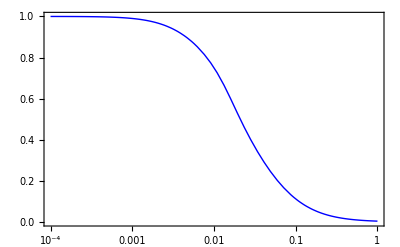

```mathematica
LogLinearPlot[tkEH[k,FoMSWG], {k, 10^-4, 1}, 
                             {Frame-> True, Axes-> False, 
                            PlotStyle-> {Thick, Blue}}]
```

#### Plot P(k)

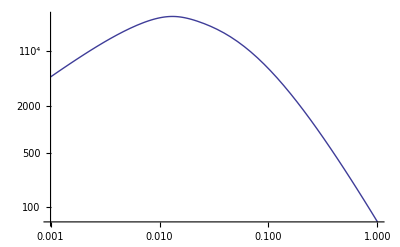

```mathematica
LogLogPlot[pkEH[k,1.0, 3. 10^-9, FoMSWG], {k, 10^-3, 1}]
```

#### Test out sigmaR on pkEH

```mathematica
pk1[k_] := pkEH[k, 1.0, 3. 10^-9, FoMSWG];
```

```mathematica
sigmaR[pk1]
```

0.819519

```mathematica
sigmaR[pk1, 8.0]
```

0.819519

```mathematica
sigmaR[pk1, 3.0]//Timing
```

{0.059231,1.45832}

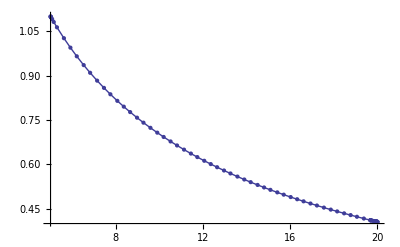

```mathematica
Plot[sigmaR[pk1, r], {r, 5.0, 20.0}, Mesh-> All]
```